```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/garrett/hg/Teaching/116/Workbook/V0/Visual-intuition-with-first-derivative

```mathematica
PolynomialFromCriticalPoints[cs_]:=With[
{der=Times@@Table[x-c,{c,cs}]},
Integrate[der,x]]
```

```mathematica
PolynomialFromCriticalPoints[{1,2,3}]
```

-6 x+(11 x^2)/2-2 x^3+x^4/4

```mathematica
GraphAndDeriv[expr_,a_,b_]:=GraphicsColumn[
{Plot[Evaluate[expr],{x,a,b},
PlotRange->{{a,b},All},
PlotRangePadding->Scaled[.05],
PlotStyle->Thick,
GridLines->Automatic,
GridLinesStyle->Directive[Gray]],
Graphics[{},
AspectRatio->1/GoldenRatio,
Ticks->{Automatic,None},
Axes->True,
PlotRange->{{a,b},{-1,1}},
PlotRangePadding->Scaled[.05],
GridLines->Automatic,
GridLinesStyle->Directive[Gray]]}]
```

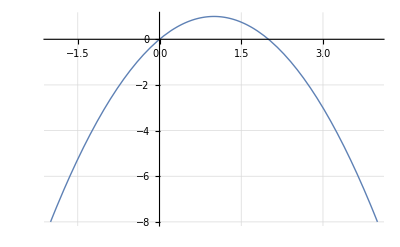

```mathematica
g1=GraphAndDeriv[-x(x-2),-2,4]
```

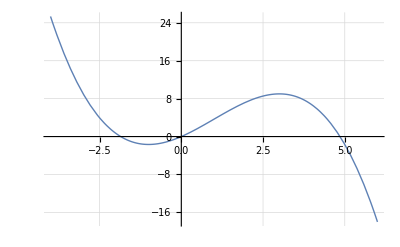

```mathematica
g2=GraphAndDeriv[-PolynomialFromCriticalPoints[{-1,3}],-4,6]
```

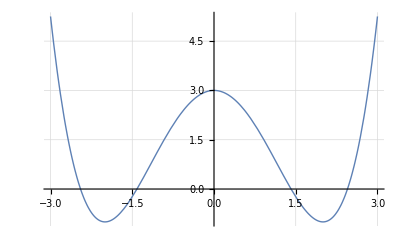

```mathematica
g3=GraphAndDeriv[PolynomialFromCriticalPoints[{2,0,-2}]+3,-3,3]
```

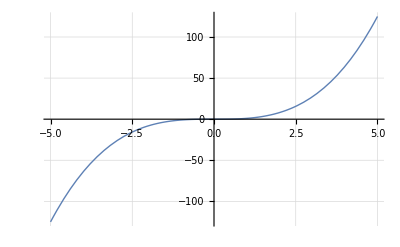

```mathematica
g4=GraphAndDeriv[x^3,-5,5]
```

```mathematica
Export["G1.pdf",g1]
```

G1.pdf

```mathematica
Export["G2.pdf",g2]
```

G2.pdf

```mathematica
Export["G3.pdf",g3]
```

G3.pdf

```mathematica
Export["G4.pdf",g4]
```

G4.pdf

```mathematica
GraphAndAntiDeriv[expr_,a_,b_]:=GraphicsColumn[
{
Graphics[{},
AspectRatio->1/GoldenRatio,
Ticks->{Automatic,None},
Axes->True,
PlotRange->{{a,b},{-1,1}},
PlotRangePadding->Scaled[.05],
GridLines->Automatic,
GridLinesStyle->Directive[Gray]],
Plot[Evaluate[expr],{x,a,b},
PlotRange->{{a,b},All},
PlotRangePadding->Scaled[.05],
PlotStyle->{Thick,Orange},
GridLines->Automatic,
GridLinesStyle->Directive[Gray]]}]
```

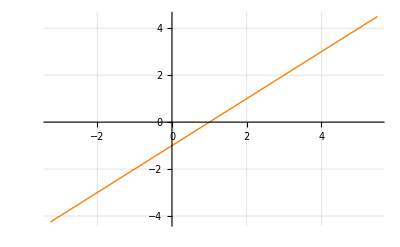

```mathematica
h1=GraphAndAntiDeriv[x-1,-3.25,5.5]
```

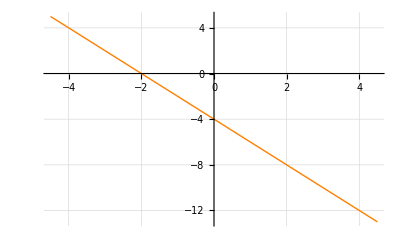

```mathematica
h2=GraphAndAntiDeriv[-2x-4,-4.5,4.5]
```

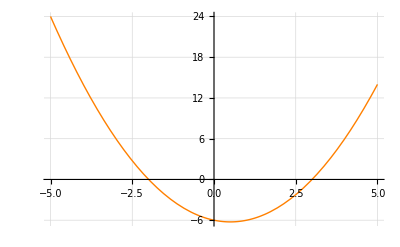

```mathematica
h3=GraphAndAntiDeriv[(x+2)(x-3),-5,5]
```

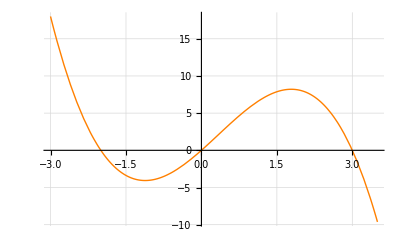

```mathematica
h4=GraphAndAntiDeriv[-(x+2)(x-3)x,-3,3.5]
```

```mathematica
Export["H1.pdf",h1]
```

H1.pdf

```mathematica
Export["H2.pdf",h2]
```

H2.pdf

```mathematica
Export["H3.pdf",h3]
```

H3.pdf

```mathematica
Export["H4.pdf",h4]
```

H4.pdf